# 2 States Mixing

```mathematica
E1=-11.13;
E2=E1+0.28;
V=2;
M={{E1, V},{V,E2}};
G=Eigensystem[M]
G[[2,1,1]]^2
```

{{-12.9949,-8.98511},{{-0.731379,0.681972},{-0.681972,-0.731379}}}

0.534915

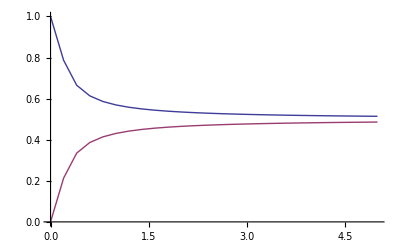

```mathematica
ListPlot[
{Table[
M1={{E1, V1},{V1,E2}};
G1=Eigensystem[M1];
{V1,G1[[2,1,1]]^2},{V1,0,5,0.2}
],
Table[
M1={{E1, V1},{V1,E2}};
G1=Eigensystem[M1];
{V1,G1[[2,1,2]]^2},{V1,0,5,0.2}
]
},Joined->True,PlotRange->All]
```

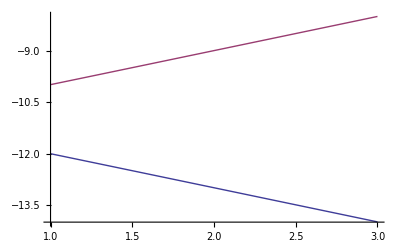

```mathematica
ListPlot[
{Table[
M1={{E1, V1},{V1,E2}};
G1=Eigensystem[M1];
{V1,G1[[1,1]]},{V1,1,3,0.2}
],
Table[
M1={{E1, V1},{V1,E2}};
G1=Eigensystem[M1];
{V1,G1[[1,2]]},{V1,1,3,0.2}
]}
,Joined->True,PlotRange->All]
```

# 3 States Mixing

```mathematica
E1=-11.13;
E2=E1+0.28;
E3=E1+1.73;
V12=2;
V23=1;
V31=0;
M={{E1, V12,V31},{V12,E2,V23},{V31,V23,E3}};
G=Eigensystem[M]
G[[2,1,1]]^2
```

{{-13.1243,-9.86175,-8.39399},{{-0.695728,0.693732,-0.186274},{0.551475,0.349705,-0.757352},{0.460259,0.629636,0.625875}}}

0.484038

```mathematica
Manipulate[
ListPlot[
{Table[
M1={{E1, V1,V3},{V1,E2,V2},{V1,V3,E3}};
G1=Eigensystem[M1];
{V1,G1[[2,1,1]]^2},{V1,0,5,0.1}
],
Table[
M1={{E1, V1,V3},{V1,E2,V2},{V1,V3,E3}};
G1=Eigensystem[M1];
{V1,G1[[2,1,2]]^2},{V1,0,5,0.1}
],
Table[
M1={{E1, V1,V3},{V1,E2,V2},{V1,V3,E3}};
G1=Eigensystem[M1];
{V1,G1[[2,1,3]]^2},{V1,0,5,0.1}
]
},Joined->True,PlotRange->All],
{V2,0,3},
{V3,0,3}]
```

```mathematica
Manipulate[
ListPlot[
{Table[
M1={{E1, V1,V3},{V1,E2,V2},{V1,V3,E3}};
G1=Eigensystem[M1];
{V1,G1[[1,1]]},{V1,0,5,0.1}
],
Table[
M1={{E1, V1,V3},{V1,E2,V2},{V1,V3,E3}};
G1=Eigensystem[M1];
{V1,G1[[1,2]]},{V1,0,5,0.1}
],
Table[
M1={{E1, V1,V3},{V1,E2,V2},{V1,V3,E3}};
G1=Eigensystem[M1];
{V1,G1[[1,3]]},{V1,0,5,0.1}
],
Table[{V1,-13.26},{V1,0,5,0.1}],
Table[{V1,-13.26+2.27},{V1,0,5,0.1}]
},Joined->True,PlotRange->All],
{V2,0,3},
{V3,0,3}]
```

# Configuration Mixing